```mathematica
M = 1;
zeta = 1;
f[t_,a_,zeta_,M_]:=(2/M) t^2 MittagLefflerE[2-a,3,-(zeta/M) t^(2-a)];
G[t_,a_,zeta_,M_]:=t MittagLefflerE[2-a,2,-(zeta/M) t^(2-a)];
G2[t_,a_,zeta_,M_]:=(t MittagLefflerE[2-a,2,-(zeta/M) t^(2-a)])^2;
h[G_,t_,a_,zeta_,M_]=Integrate[G[t,a,zeta,M],t];
h2[G2_,t_,a_,zeta_,M_]=Integrate[G2[t,a,zeta,M],t];
x[G_,t_,a_,zeta_,M_,v0_,x0_]:=x0+v0*G[t,a,zeta,M];
x2[f_,G_,t_,a_,zeta_,M_,v0_]:=(v0 -1) (G[t,a,zeta,M])^2 + f[t,a,zeta,M];
```

```mathematica
2*h[G,1,0.1,1,1]
f[1,0.1,1,1]
```

0.907164

0.907164

```mathematica
G[1,0.1,1,1]*G[1,0.1,1,1]
G2[1,0.1,1,1]
```

0.676707

0.676707

```mathematica
Evaluate[h2[G2,t,0.1,1,1]]
```

∫t^2 MittagLefflerE[1.9,2,-t^1.9]^2ⅆt

```mathematica
K
```

-(2 π t^3 FoxH[{{{0,1},{(1+a)/(-2+a),1}},{{1/2,1}}},{{{0,1}},{{-2,2-a},{1/2,1},{3/(-2+a),1}}},-t^(2-a)])/(-2+a)

```mathematica
lt=0;
length=100;
plotpoints=Table[{t,K[f,t,0.01,1,1]},{t,lt,lt+length,0.1}];
ListPlot[plotpoints]
```

Integrate::ilim: Invalid integration variable or limit(s) in 0..

Integrate::ilim: Invalid integration variable or limit(s) in 0.1.

Integrate::ilim: Invalid integration variable or limit(s) in 0.2.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

-Graphics-

```mathematica
h[x_]=Integrate[Sin[x],x];
f[h_,x_]:=h[x]-constant;
constant=1;  (*Optional:Assign the constant a value*)
f[h,0]     
h[0]
```

-2

-1

```mathematica
x2[f,G,1000,0.01,1,100,3]
```

45.0409

```mathematica
G[1000,0.01,1,1000]
```

-8.57354

```mathematica
x[G,10,0.01,1,100,3,0]
```

25.2933

```mathematica
G
```

G

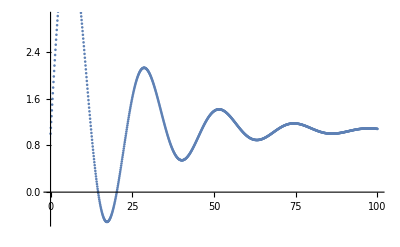

```mathematica
lt=0;
length=100;
plotpoints=Table[{t,x[G,t,0.2,1,10,1,1]},{t,lt,lt+length,0.1}];
ListPlot[plotpoints]
```

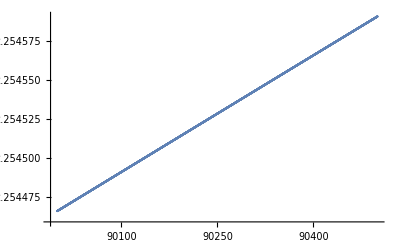

```mathematica
lt=90000;
length=500;
plotpoints=Table[{t,f[t,0.01,1,100]},{t,lt,lt+length,0.1}];
ListPlot[plotpoints]
```

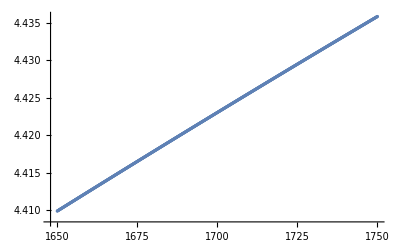

```mathematica
lt=1650;
length=100;
plotpoints=Table[{t,f[t,0.1,1,1]},{t,lt,lt+length,0.1}];
ListPlot[plotpoints]
```

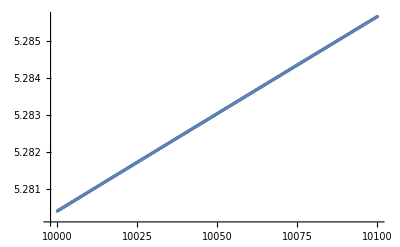

```mathematica
lt=10000;
length=100;
plotpoints=Table[{t,f[t,0.1,1,10]},{t,lt,lt+length,0.1}];
ListPlot[plotpoints]
```

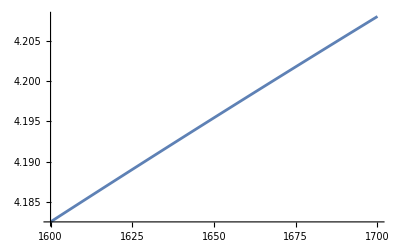

```mathematica
Plot[2 t^0.1,{t,1600,1700}]
```